```mathematica
Clear["Global`*"]
SetDirectory["/Users/brycemorsky/Desktop/New projects/Norms and pandemics/figures"];
SetOptions[{Plot,ParametricPlot,ListPlot,ListLinePlot,ListPlot3D},PlotTheme->"Vibrant",BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->Thickness[0.008]];
```

```mathematica
g[p_]=1-η*p;
g[p_]=1/(1+p*η);
u[i_,p_,q_,c_] = -β*g[p]*i-c*p-θ*(p-q)^2;
BRD[i_,p_,c_]=1/(1+Exp[κ*(u[i,0,p,c]-u[i,1,p,c])])-p;
RD[i_,p_,c_]=p*(1-p)*(u[i,1,p,c]-u[i,0,p,c]);
SEIRS={s1'[t]==-β*g[p1[t]]*s1[t]*(i1[t]+i2[t])+α*(1-s1[t]-s2[t]-e1[t]-e2[t]-i1[t]-i1[t]-r2[t]),s2'[t]==-β*g[p2[t]]*s2[t]*(i1[t]+i2[t])+α*(1-s1[t]-s2[t]-e1[t]-e2[t]-i1[t]-i1[t]-r1[t]),e1'[t]==β*g[p1[t]]*s1[t]*(i1[t]+i2[t])-δ*e1[t],e2'[t]==β*g[p2[t]]*s2[t]*(i1[t]+i2[t])-δ*e2[t],i1'[t]==δ*e1[t]-γ*i1[t],i2'[t]==δ*e2[t]-γ*i2[t],p1'[t]== ϵ*RD[i1[t]+i2[t],p1[t],c1],p2'[t]== ϵ*RD[i1[t]+i2[t],p2[t],c2]};
ics={e1[0]==0,e2[0]==0,i1[0]==0.005,i2[0]==0.005,p1[0]==0.01,p2[0]==0.01};
```

```mathematica
J=D[{-β*g[p1]*s1*(i1+i2)+α*r1,-β*g[p2]*s2*(i1+i2)+α*(1-s1-s2-e1-e2-i1-i2-r1),β*g[p1]*s1*(i1+i2)-δ*e1,β*g[p2]*s2*(i1+i2)-δ*e2,δ*e1-γ*i1,δ*e2-γ*i2,γ*i1-α*r1,ϵ*RD[i1+i2,p1,c1],ϵ*RD[i1+i2,p2,c2]},{{s1,s2,e1,e2,i1,i2,r1,p1,p2}}]/.{s1->1,s2->0,e1->0,e2->0,i1->0,i2->0,r1->0,p1->1,p2->1}
```

{{0.,0,0,0,-0.0164,-0.0164,0.01,0.,0},{-0.01,-0.01,-0.01,-0.01,-0.0756,-0.0756,-0.01,0,0.},{0.,0,-0.2,0,0.0164,0.0164,0,0.,0},{0,0.,0,-0.2,0.0656,0.0656,0,0,0.},{0,0,0.2,0,-0.1,0,0,0,0},{0,0,0,0.2,0,-0.1,0,0,0},{0,0,0,0,0.1,0,-0.01,0,0},{0,0,0,0,0.,0.,0,-4 (0.-c1+θ),0},{0,0,0,0,0.,0.,0,0,-4 (0.-2 c1+θ)}}

```mathematica
eqs=FullSimplify[Solve[{-β*g[p1]*s1*(i1+i2)+α*r1==0,-β*g[p2]*s2*(i1+i2)+α*(1-s1-s2-e1-e2-i1-i2-r1)==0,β*g[p1]*s1*(i1+i2)-δ*e1==0,β*g[p2]*s2*(i1+i2)-δ*e2==0,δ*e1-γ*i1==0,δ*e2-γ*i2==0,γ*i1-α*r1==0,ϵ*RD[i1+i2,p1,c1]==0,ϵ*RD[i1+i2,p2,c2]==0},{s1,s2,e1,e2,i1,i2,r1,p1,p2}]];
```

$Aborted

```mathematica
(* Parameters *)
α=0.01;
β=0.41;
γ=0.1;
δ=0.2;
ϵ=4;
κ=100;
η=2;
c2=2*c1;
```

```mathematica
eqs=NSolve[{-β*g[p1]*s1*(i1+i2)+α*r1==0,-β*g[p2]*s2*(i1+i2)+α*r2==0,β*g[p1]*s1*(i1+i2)-δ*e1==0,β*g[p2]*s2*(i1+i2)-δ*e2==0,δ*e1-γ*i1==0,δ*e2-γ*i2==0,γ*i1-α*r1==0,γ*i2-α*r2==0,ϵ*RD[i1+i2,p1,c1]==0,ϵ*RD[i1+i2,p2,c2]==0}/.{c1->2/100,θ->6/100},{s1,s2,e1,e2,i1,i2,r1,r2,p1,p2},Reals,WorkingPrecision->15];
```

```mathematica
{-β*g[p1]*s1*(i1+i2)+α*r1,-β*g[p2]*s2*(i1+i2)+α*(1-s1-s2-e1-e2-i1-i2-r1),β*g[p1]*s1*(i1+i2)-δ*e1,β*g[p2]*s2*(i1+i2)-δ*e2,δ*e1-γ*i1,δ*e2-γ*i2,γ*i1-α*r1,ϵ*RD[i1+i2,p1,c1],ϵ*RD[i1+i2,p2,c2]}/.{c1->1/100,θ->2/100}/.{s1->0.7,s2->0.3,e1->0,e2->0,i1->0,i2->0,r1->0,p1->1,p2->1}
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
M=Array[m,{100,3}];
count=1;
Do[
M[[count]]={x/100,y/100,FromDigits[Boole[Map[AllTrue[#,#<0&,1]&,Map[Re[#]&,Eigenvalues[J/.{θ->x/100,c1->y/100}]]]],2]};
count=count+1;
,{x,1,100},{y,1,100}];
DeleteDuplicates[M[[All,3]]]
```

{511}

```mathematica
BaseForm[511,2]
```

111111111_2

```mathematica
M
```

{{1/10,1/10,Boole[Eigenvalues[{0,0,0,0,0.,0.,0,0,0.4}]<0]+2 (Boole[Eigenvalues[{0,0,0,0,0.,0.,0,0.,0}]<0]+2 (Boole[Eigenvalues[{0,0,0,0,0.1,0,-0.01,0,0}]<0]+2 (Boole[1]+1)))},98,{1,1,Boole[Eigenvalues[{1}]<0]+2 1}}
 |  |  |  |

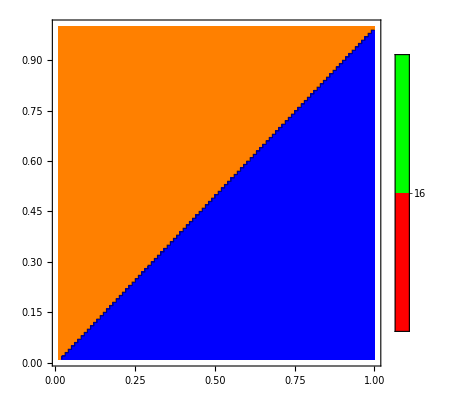

```mathematica
ListContourPlot[M,Contours->{0,4,12,20},ContourShading->{Blue,Red,Green,Orange},PlotLegends->Automatic]
```

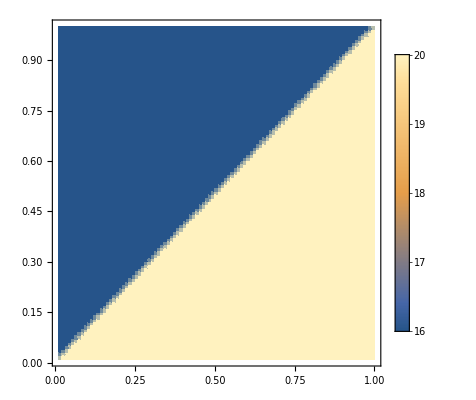

```mathematica
ListDensityPlot[M,PlotLegends->Automatic]
```

```mathematica
h1=Boole[Map[AllTrue[#,#<0&,1]&,Map[Re[#]&,Map[Eigenvalues[#]&,J/.{θ->80/100,c->20/100}]]]]
h2=Boole[Map[AllTrue[#,And[0≤#≤ 1,MatchQ[#,_Real]]&,1]&,{s,e,i,p}/.eqs/.{θ->80/100,c->20/100}]]
h1 h2
{s,e,i,p}/.eqs[[2;;7]]/.{θ->80/100,c->20/100}
Map[Eigenvalues[#]&,J/.{θ->80/100,c->20/100}]
```

{0,1,0,1,0,0}

{1,1,1,1,1,1}

{0,1,0,1,0,0}

{s,e,i,p}/.{{s→1.,e→0.,i→0.,p→0.},{s→0.243902,e→0.0328738,i→0.0657476,p→0.},{s→1.,e→0.,i→0.,p→1.},{s→0.439024,e→0.0243902,i→0.0487805,p→1.},{s→0.364626,e→0.027625,i→0.0552499,p→0.618708},{s→1.,e→0.,i→0.,p→0.625}}⟦2;;7⟧

{{-4.,-0.440689,0.140689,-0.01},{-3.95208+0. ⅈ,-0.306504+0. ⅈ,-0.0152261+0.0423199 ⅈ,-0.0152261-0.0423199 ⅈ},{-2.4,-0.369216,0.0692158,-0.01},{-2.43556+0. ⅈ,-0.302605+0. ⅈ,-0.00925285+0.0275482 ⅈ,-0.00925285-0.0275482 ⅈ},{1.50978+0. ⅈ,-0.303769+0. ⅈ,-0.0106736+0.0321118 ⅈ,-0.0106736-0.0321118 ⅈ},{1.5,-0.389096,0.0890955,-0.01}}

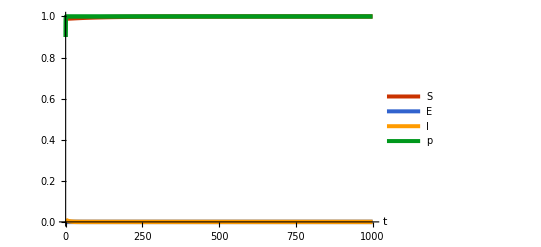

```mathematica
sol=NDSolve[Join[SEIRS/.{c->0.1,θ->0.8},{s[0]==0.99,e[0]==0,i[0]==0.01,p[0]==0.01}],{s,e,i,p},{t,0,1000}];
Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,1000},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
```